## EdgesOnTop-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 12:11:50
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

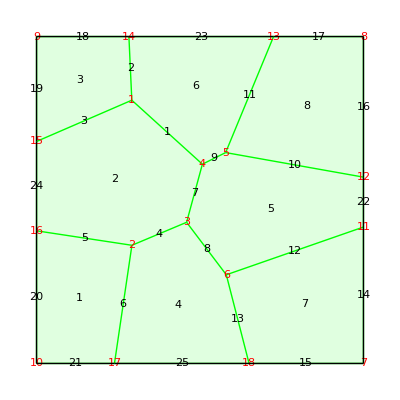

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

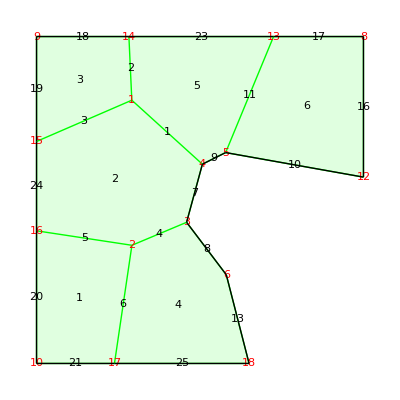

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
S=DTissue2Tissue[R];
ShowTissue[S, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

```mathematica
VertexOutwardNormal[S,3, True]
```

{0.480754,0.23971}

```mathematica
VerticesOnTop[S]
```

{8,13,14,9,6}

```mathematica
CellsOnLeft[R]
```

{1,2,3}

```mathematica
CellsOnBottom[R]
```

{1,4,6}

```mathematica
EdgesOnTop[S]
```

{17,18,23}

```mathematica
EdgesOnLeft[S]
```

{19,20,24}

```mathematica
VerticesOnLeft[R]
```

{9,15,16,10}

```mathematica
CellsOnBottom[S]
```

{1,4,6}